We consider the scenario as described in the following picture

```mathematica
Import[FileNameJoin[{NotebookDirectory[],"setup.png"}]]
```

-Graphics-

We have block (which one might imagine to be a piece of bread) with thickness b and length l. Assume the block to move on a table towards the edge. We call the distance between the center of mass of the block and the rotation point on a table s[t] and the angle between the horizontal line and the block θ[t]. We want to predict the trajectory of the block.

```mathematica
ClearAll["Global`*"]
```

```mathematica
(*We first parametrize the above scenario in a 2D coordinate system with origin in the point of rotation*)
x[t_]={{s[t] Cos[θ[t]]+b/2 Sin[θ[t]]},{-s[t] Sin[θ[t]]+b/2 Cos[θ[t]]}};
```

```mathematica
(*We now input all the parameters that describe the problem, i.e. the mass m, length l, thickness b and the moment of inertia J of the block*)
m=0.1;l=0.1;g=9.81; b=0.02;
J=1.0/12.0 m (l^2+b^2);
```

```mathematica
(*The next step is to determine the equations of motion. We use the Lagrangian formalism for this*)
<<VariationalMethods`
```

```mathematica
(*T: Kinetic energy; V: Potential energy; L: Lagrangian*)
T[t_]=1.0/2.0 (m) Flatten[x'[t]].Flatten[x'[t]]+1.0/2.0 J θ'[t]^2;
V[t_]=m g x[t][[2,1]];
L[t_]=T[t]-V[t]//Simplify;
```

```mathematica
(*We now use the VariationalMethods package to perform the functional derivatives and obtain the equations of motion*)
eoms[t_]=VariationalD[L[t],s[t],t]//Simplify;
eomθ[t_]=VariationalD[L[t],θ[t],t]//Simplify;
```

```mathematica
(*To find the solutions of the equations of motion we need to set the initial condtions*)
exampleVelocity=0.4;
PDESolver[speed_]:=NDSolve[{eoms[t]==0.0,eomθ[t]==0.0,θ[0]==0,s[0]==0.01,s'[0]==speed,θ'[0]==0.1},{θ,s},{t,0.0,2.0}];
exampleSolution=PDESolver[exampleVelocity];
```

These solutions only make sense up to the time when the block would lose contact to the table. We need to find this time.

```mathematica
(*The block loses contact to the table when (x''[t])_x ==0*)
f[t_]=D[x[t][[1,1]],{t,2}]/.exampleSolution;
tLoseContactTable=t/.FindRoot[f[t],{t,0.1}];
(*
f[t_]=D[θ[t],{t,2}]/.exampleSolution;
tLoseContactTable=t/.FindRoot[f[t],{t,0.1}];
*)
```

After this tLoseContactTable the block just freely falls, i.e. the angular velocity will stay constant and the translational velocity will only be changed by gravity. We can therefore just write down the exact solution to the problem.

```mathematica
(*Trajectory of the Center of mass before the contact is lost*)
trajectory[t_]:=Flatten[x[t]/.exampleSolution];
(*Velocity vector of center of mass*)
velocity[t_]=Flatten[D[trajectory[t],t]];
```

```mathematica
(*
I call the following function the way I do because it's the standard way of calling the parabola that an objects takes when thrown, 
and the only force acting on it is gravity---in German. I will leave out the mathematics here.. A piece of paper and a couple of 
minuest playing around with elementrary ODE's will give a result equivalent to this one. The "hard" part is determining x0 and y0, 
since they need to properly link to the solution obtained numericaly.*)
Wurfparabel[time_,sol_,tZero_,vZero_]:=Module[{r0,angle,x,x0,y,y0},
angle=Abs[Flatten[θ[tZero]/.sol]];
x=vZero[[1]] time Cos[angle];
r0=trajectory[tZero]/.sol//Flatten;
x0=Abs[r0[[1]]-vZero[[1]] tZero Cos[angle]];
y=-(Norm[vZero] time Sin[angle] + g time^2/2.0);
y0=Abs[r0[[2]]+(Norm[vZero] tZero Sin[angle] + g tZero^2/2.0)];
Return[Flatten[{x0+x,y0+y}]]];
```

Let us plot the solution to see if the result makes sense

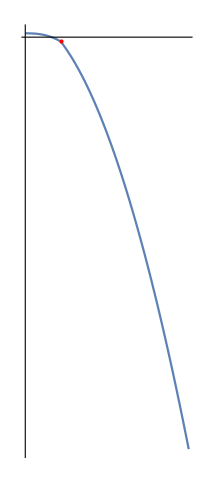

```mathematica
p1=ParametricPlot[trajectory[t],{t,0,tLoseContactTable}];
p2=ParametricPlot[Wurfparabel[t,exampleSolution,tLoseContactTable,velocity[tLoseContactTable]],{t,tLoseContactTable,0.45}];
p3 =Graphics[{PointSize[Large],Red,Point[trajectory[tLoseContactTable]]}];
Show[p1,p2, p3, PlotRange->{{-0.01,0.5},{0.01,-0.3}},Ticks->None,AspectRatio->Automatic]
```

Seems reasonable. But this is just the path that the center of mass takes. Let’s visualize the path of the block including the rotation.

```mathematica
edgesOfBread[sol_,time_,xCenter_,tContactLoss_]:=Module[{theta,angle,v,u},
theta[t_] = θ[t]/.sol;
angle=theta'[tContactLoss] time;
(*Vectors that are parallel to the vertices of the block*)
v=l/2.0{Cos[angle],-Sin[angle]};
u=b/2.0{Sin[angle],Cos[angle]};
lowerLeftCorner=Flatten[xCenter+v-u];
upperLeftCorner=Flatten[xCenter+v+u];
upperRightCorner=Flatten[xCenter-v+u];
lowerRightCorner=Flatten[xCenter-v-u];
Return[{lowerLeftCorner,upperLeftCorner,lowerRightCorner,upperRightCorner}]
]
box[{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_}]:=ListLinePlot[{{{x2,y2},{x1,y1},{x4,y4},{x3,y3}},{{x2,y2},{x3,y3}}},PlotStyle->{Black,Red},Axes->None];
DrawBlock[sol_,time_]:= Module[{},
If[time<tLoseContactTable,
xCenter=trajectory[time],
xCenter=Wurfparabel[time,exampleSolution,tLoseContactTable,velocity[tLoseContactTable]]];
edges=edgesOfBread[sol,time,xCenter,tLoseContactTable];
Return[box[edges[[3]],edges[[4]],edges[[2]],edges[[1]]]]];
(*We also want to draw in the table, so we need to fix the table-height*)
exampleTabelHeight=1.3;
tabel =Graphics[{Pink,Rectangle[{-1,-exampleTabelHeight},{0.01,0}]}];
turningPoint =Graphics[{PointSize[Large],Blue,Point[{0.01,0}]}];
```

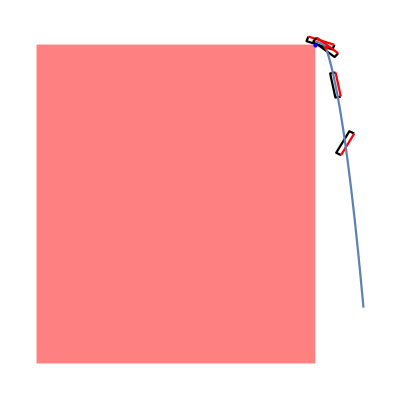

```mathematica
Show[
Graphics[DrawBlock[exampleSolution,tLoseContactTable/2]],
Graphics[DrawBlock[exampleSolution,tLoseContactTable]],
Graphics[DrawBlock[exampleSolution,tLoseContactTable*2]],
Graphics[DrawBlock[exampleSolution,tLoseContactTable*3]],
p1,p2,p3,tabel,turningPoint,
PlotRange-> {{-0.1,1},{0.1,-exampleTabelHeight}},AspectRatio->1]
```

At this point an interesting question might be: Substituting the block with a piece of toast, will the butter-side land on the floor or not? This depends on bscly. two parameters: the height of the table and the speed with which the bread starts. We therefore first need a function that determines if a solution will land on the butter side or not. We split the problem in several sub-tasks: 1.) We figure out what after how many seconds the Bread lands on the ground. 2.) We evolve the system up to that point and then determine if the butter side is pointing upwards or not. The following two functions take care of the first task.

```mathematica
lowestPositionBread[time_,sol_,xCenter_,tContactLoss_]:=Module[{},
Return[Abs[Min[edgesOfBread[sol,time,xCenter,tContactLoss]]]]];
```

```mathematica
timeBreadAtGround[height_,sol_,tContactLoss_]:=Module[{},
trajectory[t_]:=Flatten[x[t]/.sol];
tGround=t/.FindRoot[height-lowestPositionBread[t,sol,trajectory[t],tContactLoss],{t,0.3}];
Return[tGround];
]
```

We are left with task 2.), which is probably the hardest part. We first determine the total angle the bread has travelled when its lowest point hits the ground.

```mathematica
AngleAtGround[sol_,tZero_,tGround_]:=Module[{},
theta[t_]=Flatten[θ[t]/.sol];
θ0=Abs[theta[tZero]-theta'[tZero] tZero+theta[tZero]];
angle=theta'[tZero] tGround-theta[tZero]+θ0;
Return[Mod[angle[[1]],2.0 Pi]]];
```

If the angle is between π/2 and 3π/2, the bread lands on the butter side. Obviously, the bread could spin around more than once, we therefore take the θ mod 2π. We now  write a simple function that returns either 0 or 1, depending on if the bread lands on the butter side or not.

```mathematica
(*Returns 1.0 for ButterSide and 0.0 if not*)
BreadOrButterSide[phi_]:=
If[Pi/2.0≤phi,
If[phi≤3.0 Pi/2.0,1.0,0.0],
0.0];
```

We now put everything together

```mathematica
(*StartingValueList is an vector of the form {speed, height}*)
ClearAll[solution]
goodStartIntoDay[StartingValuesList_]:=Module[{},
solution=PDESolver[StartingValuesList[[1]]];
f[t_]=D[θ[t],{t,2}]/.solution;
tContactLoss=t/.FindRoot[f[t],{t,0.1}];
tGround = timeBreadAtGround[StartingValuesList[[2]],solution,tContactLoss];
ϕ=AngleAtGround[solution,tContactLoss,tGround];
Return[BreadOrButterSide[ϕ]];
]
```

We can now generate tuples of the form (initial bread velocity, table height) and then evaluate each of them on “goodStartIntoDay”. We also write a nice function to monitor and time the progress of the calculation.

```mathematica
(*Added a Progress Bar to the Map function*)
MapMonitored[f_,args_List]:=Module[{x=0},Monitor[MapIndexed[(x=#2[[1]];f[#1])&,args],ProgressIndicator[x/Length[args]]]]
```

```mathematica
velocities=Array[#&,75,{0.01,1.8}];
TabelHeights=Array[#&,40,{0.2,2.5}];
mesh=Tuples[{velocities,TabelHeights}];
```

```mathematica
plotmesh=MapMonitored[goodStartIntoDay,mesh]//AbsoluteTiming;
Print["Computation time ",plotmesh[[1]]," sec"]
```

Computation time 12.6344 sec

```mathematica
PointsOfInterest=GroupBy[Thread[{mesh,plotmesh[[2]]}],Last->First];
```

```mathematica
<<MaTeX`
```

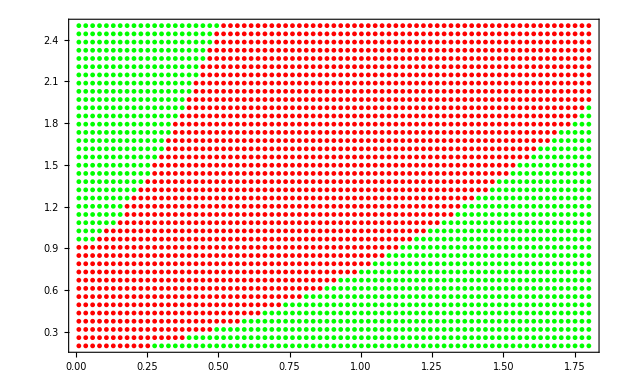

```mathematica
pic=Show[{
ListPlot[PointsOfInterest[[1]],PlotStyle->Red],
ListPlot[PointsOfInterest[[2]],PlotStyle-> Green]},
PlotRange->All,
Frame->True,
FrameLabel->MaTeX/@{"v~[m/s]","h~[m]"}
]
```

```mathematica
Export["height_vs_speed.pdf",pic]
```

height_vs_speed.pdf

In the above plot the red area signals that the these initial conditions will lead to the bread landing on the butter side, while the green initial conditions will make sure that you still can enjoy your bread.